Scattering from the cavity mirrors vs the RMS roughness. For some reason I’m taking the square root of the mirror reflectivity... not sure if this is valid. Not clear if this is a helpful calculation as is, because it does not calculate the fraction of scattering which leaves the mode, from which we could estimate how the finesse would change due to this loss.

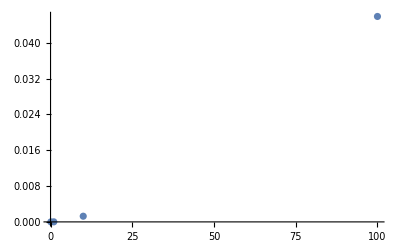

```mathematica
nm=10^-9;
w0=5*^-6;(*cavity waist*)
λ=7.8*^-7;
t=ArcSin[λ/(π w0)]/2;(*half angle spanned by cavity mode*)
Rlow=1-4620/10^6;(*using Thigh from network paper, 4mm cav*)
Rhigh = 1-10/10^6;(*using Tlow from network paper, 4mm cav*)
(*integrand from https://www.eckop.com/resources/scatterometer-resources/optical-scattering-versus-surface-roughness/*)
ListPlot[Evaluate[Table[{Rq/nm,√(Rhigh Rlow)NIntegrate[(1-Exp[-(4π Rq Cos[θ]/λ)^2]),{θ,-t,t}]},{Rq,{0.1 nm,1nm,10nm,100nm}}]]]
```

```mathematica
NIntegrate[(1-Exp[-(4π 0.1 Cos[θ]/λ)^2]),{θ,-t,t}]/.Rq->0.1
```

0.0496768

```mathematica
NIntegrate[Exp[-(4π 0.1 Cos[θ]/λ)^2],{θ,-t,t}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
t
```

```mathematica
Clear[λ,t]
Integrate[1-Exp[-(4π Rq Cos[θ]/λ)^2],{θ,-t,t}]
```

∫_-t^t (1-ⅇ^(-(16 π^2 Rq^2 Cos[θ]^2)/λ^2))ⅆθ